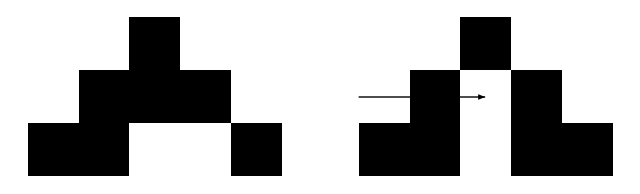

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[30,{{1},0},{2, {-2, 2}}]], Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ [30,{{1},0},{2, {-2, 2}}, {1, 3}->0]]}]
```